## global setting

```mathematica
SetDirectory[NotebookDirectory[]];
sootsize=0.5;
hairsize=0.25;
firstframesize={{0.1,0.18},{0.3,0.28}};
firstframe2position={{0.01,0.5},{0.5,0.99}};
PAHsize1=0.05;
PAHclusterstep=0.03;
aliphaticsize=1.11*PAHsize1;
largePAHsize=0.098;
Hbondsize=0.03;
Hatomcolor={GrayLevel[0],Red};
CCbondsize=largePAHsize/√3;
doublebondspace=0.0085;
framecolor=White;
keycolor=Purple;
frameedgecolor={Purple,Thick};
opacitydeg=0;
opacitykey=0.25;
```

## paintsheet

```mathematica
paintsheet=Graphics[{Opacity[0],EdgeForm[{Black,Thick}],White,Polygon[{{0,0},{1,0},{1,1},{0,1}}]},PlotRange-> {{-0.01,1.01},{-0.01,1.01}}];
```

## soot particle

```mathematica
sootparticle=Graphics[   {     Disk[{0,0},{sootsize,sootsize/2},{0,Pi/2} ]}  ];
```

```mathematica
sootword=Graphics[Text[Style["SOOT",{30,Bold,Gray}],{sootsize/2.5,sootsize/5}]];
```

```mathematica
sootedge[x_]:={x,sootsize/2*√(1-x^2/sootsize^2)};
```

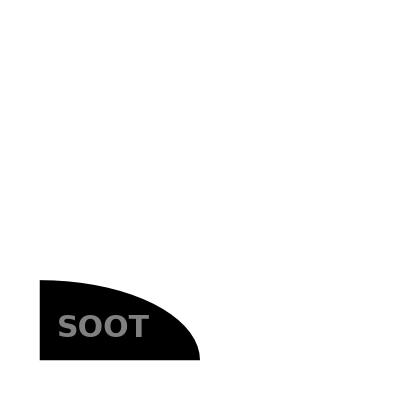

```mathematica
Show[paintsheet,sootparticle,sootword]
```

## hair

```mathematica
(*onehair[coor_,dire_]:=BezierFunction[{coor,coor+0.1*{dire⟦1⟧,dire⟦2⟧/2},coor+0.2*dire,coor+0.3*{dire⟦1⟧/2,dire⟦2⟧}}]*)
```

```mathematica
pts={{0,0},{1,1},{2,-1},{3,0}}/3*hairsize;
```

```mathematica
ListPlot[pts,PlotMarkers-> {Automatic,Large}];
```

```mathematica
Table[RotationMatrix[Pi/2].pts⟦i⟧,{i,1,Length[pts]}];
```

```mathematica
ListPlot[Table[RotationMatrix[Pi/2].pts⟦i⟧,{i,1,Length[pts]}],PlotMarkers-> {Automatic,Large}];
```

```mathematica
onehair[coor_,theta_]:= ParametricPlot[
                                                                BezierFunction[
                                                                     Table[RotationMatrix[theta].pts⟦i⟧+coor,{i,1,Length[pts]}]
                                                              ]
                                                       [t],{t,0,1},PlotStyle-> {Thick,Blue}];
```

```mathematica
(*hairtry=Graphics[ParametricPlot[onehair[{0,0.25},{1/√2,1/√2}][t],{t,0,1}]]*)
```

```mathematica
onehair[sootedge[0],Pi/2 ];
```

```mathematica
(*hairs=Table[onehair[sootedge[Random[]/2],Random[]*Pi/2 ],{i,1,5}]*)
```

```mathematica
aa={0.08,0.2,0.34,0.38,0.47};
bb={0.9,0.7,0.3,0.6,0.95};
hairs=Table[onehair[sootedge[aa⟦i⟧],bb⟦i⟧*Pi/2 ],{i,1,5}];
```

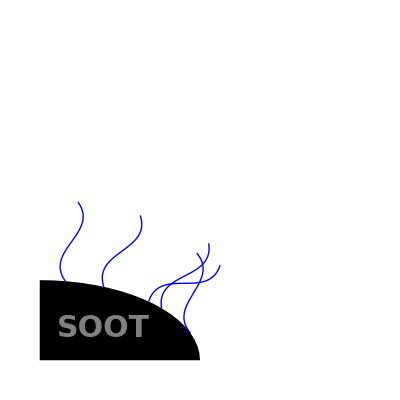

```mathematica
Show[paintsheet,sootparticle,sootword,hairs]
```

## first frame

```mathematica
firstframe=Graphics[{Opacity[opacitydeg],EdgeForm[frameedgecolor],framecolor,Rectangle[firstframesize⟦1⟧,firstframesize⟦2⟧]}];
```

```mathematica
firstframe2=Graphics[{Opacity[opacitydeg],EdgeForm[frameedgecolor],framecolor,Rectangle[firstframe2position⟦1⟧,firstframe2position⟦2⟧]}];
```

```mathematica
linkfirstframes=Graphics[{{Red,Dashed,Line[{{firstframesize⟦1,1⟧,firstframesize⟦2,2⟧},{firstframe2position⟦1,1⟧,firstframe2position⟦1,2⟧}}]},{Red,Dashed,Line[{{firstframesize⟦2,1⟧,firstframesize⟦2,2⟧},{firstframe2position⟦2,1⟧,firstframe2position⟦1,2⟧}}]}}];
```

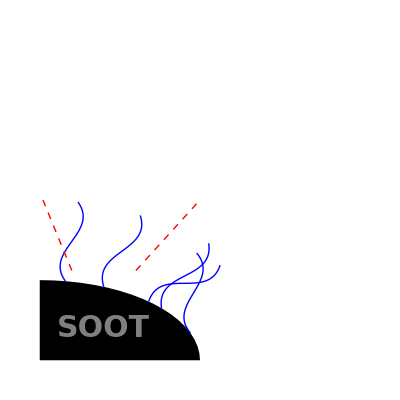

```mathematica
Show[paintsheet,sootparticle,sootword,hairs,firstframe,firstframe2,linkfirstframes]
```

## PAH

```mathematica
benzenegraph[cen_,side_,shift_]:={Opacity[1],EdgeForm[{Black}],GrayLevel[(1-0)],Polygon[{{cen⟦1⟧+shift,cen⟦2⟧+side⟦2⟧/(√3)},{cen⟦1⟧+side⟦1⟧/2+shift/2,cen⟦2⟧+side⟦2⟧/(2 √3)},{cen⟦1⟧+side⟦1⟧/2-shift/2,cen⟦2⟧-side⟦2⟧/(2 √3)},{cen⟦1⟧-shift,cen⟦2⟧-side⟦2⟧/(√3)},{cen⟦1⟧-side⟦1⟧/2-shift/2,cen⟦2⟧-side⟦2⟧/(2 √3)},{cen⟦1⟧-side⟦1⟧/2+shift/2,cen⟦2⟧+side⟦2⟧/(2 √3)}}]} ;
pahgraph[cen_,side_,zigzag_,armchair_,shift_]:= Graphics[Table[benzenegraph[{cen⟦1⟧+j*side⟦1⟧+Mod[i,2]*side⟦1⟧/2,cen⟦2⟧-i*(√3)/2*side⟦2⟧},side,shift],{i,0,armchair-1},{j,0,zigzag-1}] ];
pahgraphMultiRow[cen_,side_,zigzag_,armchair_,shift_]:=Graphics[{Table[benzenegraph[{cen⟦1⟧+k*side⟦1⟧,cen⟦2⟧},side,shift],{k,0,zigzag-1}], Table[benzenegraph[{cen⟦1⟧-IntegerPart[(2*zigzag-1-j)/(zigzag+0.2)]*side⟦1⟧/2+Mod[j+1,zigzag]*side⟦1⟧-(3*i+1/2*IntegerPart[(2*zigzag-1-j)/(zigzag+0.2)]+2*IntegerPart[(j+1)/(zigzag-0.2)]+1)*shift,cen⟦2⟧-(2*i+1)*(√3)/2*side⟦2⟧-IntegerPart[(j+1)/(zigzag-0.2)]*(√3)/2*side⟦2⟧},side,shift],{i,0,(armchair-3)/2},{j,0,zigzag*2-2}] }];
pahgraphMultiRow2[cen_,side_,zigzag_,armchair_,shift_]:={Table[benzenegraph[{cen⟦1⟧+k*side⟦1⟧,cen⟦2⟧},side,shift],{k,0,zigzag-1}], Table[benzenegraph[{cen⟦1⟧-IntegerPart[(2*zigzag-1-j)/(zigzag+0.2)]*side⟦1⟧/2+Mod[j+1,zigzag]*side⟦1⟧-(3*i+1/2*IntegerPart[(2*zigzag-1-j)/(zigzag+0.2)]+2*IntegerPart[(j+1)/(zigzag-0.2)]+1)*shift,cen⟦2⟧-(2*i+1)*(√3)/2*side⟦2⟧-IntegerPart[(j+1)/(zigzag-0.2)]*(√3)/2*side⟦2⟧},side,shift],{i,0,(armchair-3)/2},{j,0,zigzag*2-2}] }
```

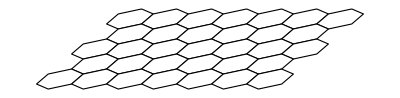

```mathematica
Show[pahgraphMultiRow[{0,0},{1,0.5}*0.03,7,5,0.01]]
```

## PAH cluster

```mathematica
PAHcluster[coor_,side_,zigzag_,armchair_,shift_]:=pahgraphMultiRow[coor,side*PAHsize1,zigzag,armchair,shift*PAHsize1]
```

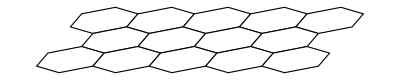
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
cluster1=Table[PAHcluster[{firstframe2position⟦1,1⟧+PAHsize1*1.5,firstframe2position⟦1,2⟧+i*PAHclusterstep},{1,0.1},5,3,0.2],{i,1,5}]
```

```mathematica
cluster2final=Table[Graphics[pahgraphMultiRow2[{firstframe2position⟦1,1⟧-PAHsize1+i*1*PAHclusterstep,firstframe2position⟦1,2⟧+9.5*PAHclusterstep-1*i*PAHclusterstep},{1,0.3}*PAHsize1,8,3,0.2*PAHsize1],PlotRange-> {{firstframe2position⟦1,1⟧,firstframe2position⟦2,1⟧},{firstframe2position⟦1,2⟧,firstframe2position⟦2,2⟧}}],{i,3,1}];
```

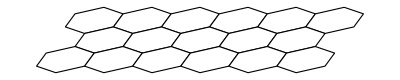
{-Graphics-,-Graphics-,-Graphics-}

```mathematica
cluster2=Table[PAHcluster[{firstframe2position⟦1,1⟧+0.5*PAHsize1+i*1*PAHclusterstep,firstframe2position⟦1,2⟧+9.5*PAHclusterstep-1*i*PAHclusterstep},{1,0.3},6,3,0.2],{i,3,1,-1}]
```

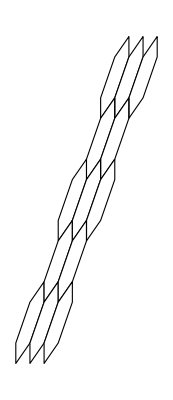
{-Graphics-,-Graphics-,-Graphics-}

```mathematica
cluster3=Table[PAHcluster[{firstframe2position⟦1,1⟧+PAHsize1*7+i*1*PAHclusterstep,firstframe2position⟦1,2⟧+PAHsize1*4+0.3*i*PAHclusterstep},{0.2,1},3,5,0.2],{i,1,3}]
```

```mathematica
cluster4=Graphics[benzenegraph[{firstframe2position⟦1,1⟧+PAHsize1*6,firstframe2position⟦1,2⟧+PAHsize1*2},{0.3,1}*PAHsize1,-0.2*PAHsize1]];
```

```mathematica
cluster5=pahgraph[{firstframe2position⟦1,1⟧+PAHsize1*6.25,firstframe2position⟦1,2⟧+PAHsize1*2.5},{0.3,1}*PAHsize1,2,1,-0.1*PAHsize1];
```

```mathematica
cluster6=PAHcluster[{firstframe2position⟦1,1⟧-0.5*PAHsize1+4*1*PAHclusterstep,firstframe2position⟦1,2⟧+9.5*PAHclusterstep-1*(-1)*PAHclusterstep},{1,0.3},8,5,0.2];
```

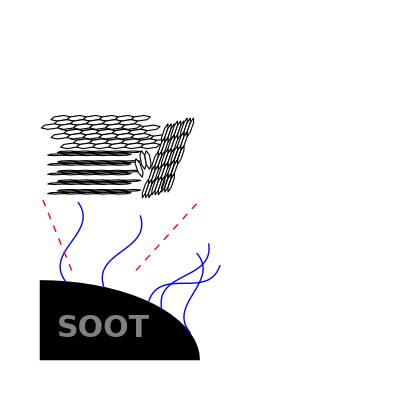

```mathematica
Show[paintsheet,sootparticle,sootword,hairs,firstframe,firstframe2,linkfirstframes,cluster1,cluster2,cluster3,cluster4,cluster5]
```

## aliphatics

```mathematica
aliphaticptsraw={{0,0},{0.5,1},{0,2},{0.5,3},{0,4}}
```

{{0,0},{0.5,1},{0,2},{0.5,3},{0,4}}

```mathematica
doublebonds1raw={{0.6,1+0.1},{0.1,2+0.1}};
doublebonds2raw={{0.6,3+0.1},{0.1,4+0.1}};
```

```mathematica
aliphaticpts=Table[aliphaticptsraw⟦i⟧*aliphaticsize+{firstframe2position⟦1,1⟧+2.3*PAHsize1,firstframe2position⟦1,2⟧+9.8*PAHclusterstep-1*PAHclusterstep},{i,1,Length[aliphaticptsraw]}];
```

```mathematica
doublebonds1=Table[doublebonds1raw⟦i⟧*aliphaticsize+{firstframe2position⟦1,1⟧+2.3*PAHsize1,firstframe2position⟦1,2⟧+9.8*PAHclusterstep-1*PAHclusterstep},{i,1,Length[doublebonds1raw]}];
```

```mathematica
doublebonds2=Table[doublebonds2raw⟦i⟧*aliphaticsize+{firstframe2position⟦1,1⟧+2.3*PAHsize1,firstframe2position⟦1,2⟧+9.8*PAHclusterstep-1*PAHclusterstep},{i,1,Length[doublebonds2raw]}];
```

```mathematica
aliphatic=Graphics[{Line[aliphaticpts],Line[doublebonds1],Line[doublebonds2]}];
```

```mathematica
acetylene=Graphics[{Line[{{0.35,0.85}+{0.00,0.05},{0.35,0.85}+{0.00,0.05}-PAHsize1}],Line[{{0.345,0.855}+{0.00,0.05},{0.345,0.855}+{0.00,0.05}-PAHsize1}],Line[{{0.34,0.86}+{0.00,0.05},{0.34,0.86}+{0.00,0.05}-PAHsize1}]}];
```

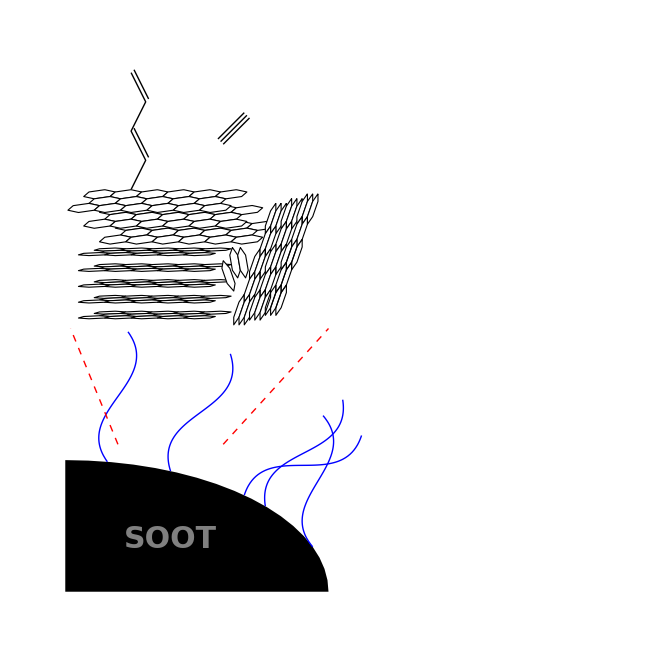

```mathematica
Show[paintsheet,sootparticle,sootword,hairs,firstframe,firstframe2,linkfirstframes,cluster1,cluster2,cluster3,cluster4,cluster5,aliphatic,acetylene]
```

## Large PAH

```mathematica
benzenegraphRot[cen_,side_]:={{Opacity[0],EdgeForm[{Black,Thickness[0.005]}],GrayLevel[(1-0)],Polygon[{{cen⟦2⟧+side/(√3),cen⟦1⟧},{cen⟦2⟧+side/(2 √3),cen⟦1⟧+side/2},{cen⟦2⟧-side/(2 √3),cen⟦1⟧+side/2},{cen⟦2⟧-side/(√3),cen⟦1⟧},{cen⟦2⟧-side/(2 √3),cen⟦1⟧-side/2},{cen⟦2⟧+side/(2 √3),cen⟦1⟧-side/2}}]} };
pahgraphRot[cen_,side_,zigzag_,armchair_]:=Graphics[ Table[benzenegraphRot[{cen⟦1⟧+j*side+Mod[i,2]*side/2,cen⟦2⟧-i*(√3)/2*side},side],{i,0,armchair-1},{j,0,zigzag-1}] ];
pahgraphMultiRowRot[cen_,side_,zigzag_,armchair_]:=Graphics[{Table[benzenegraphRot[{cen⟦1⟧+k*side,cen⟦2⟧},side],{k,0,zigzag-1}], Table[benzenegraphRot[{cen⟦1⟧-IntegerPart[(2*zigzag-1-j)/(zigzag+0.2)]*side/2+Mod[j+1,zigzag]*side,cen⟦2⟧-(2*i+1)*(√3)/2*side-IntegerPart[(j+1)/(zigzag-0.2)]*(√3)/2*side},side],{i,0,(armchair-3)/2},{j,0,zigzag*2-2}] (*,Table[Line[],{i,1,zigzag}]*)}];
pahgraphMulti2RowRot[cen_,side_,zigzag_,armchair_]:={ Table[benzenegraphRot[{cen⟦1⟧-IntegerPart[(2*zigzag-1-j)/(zigzag+0.2)]*side/2+Mod[j+1,zigzag]*side,cen⟦2⟧-(2*i+1)*(√3)/2*side-IntegerPart[(j+1)/(zigzag-0.2)]*(√3)/2*side},side],{i,0,(armchair-3)/2},{j,0,zigzag*2-2}] }
pahHatom[cen_,side_,zigzag_,armchair_,Hbond_]:={Table[Line[{{cen⟦2⟧-(2*0+1)*(√3)/2*side-IntegerPart[(i+1)/(zigzag-0.2)]*(√3)/2*side-1/(√3)*side,cen⟦1⟧-IntegerPart[(2*zigzag-1-i)/(zigzag+0.2)]*side/2+Mod[i+1,zigzag]*side},{cen⟦2⟧-(2*0+1)*(√3)/2*side-IntegerPart[(i+1)/(zigzag-0.2)]*(√3)/2*side-1/(√3)*side-Hbond,cen⟦1⟧-IntegerPart[(2*zigzag-1-i)/(zigzag+0.2)]*side/2+Mod[i+1,zigzag]*side}}],{i,zigzag-1,zigzag*2-2}]}(*]*);
```

```mathematica
(*Clear[pahgraphMulti2RowRot,pahHatom,largePAH,pahHatoms]*)
```

```mathematica
(*largePAH=pahgraphMultiRowRot[{0.06,0.81},0.098,10,3];*)
largePAH=Graphics[{Rotate[pahgraphMulti2RowRot[{0.06,0.81},largePAHsize,10,3],Pi]}];
pahHatoms1=Graphics[{Thick,Rotate[pahHatom[{0.06,1.04},0.098,10,3,Hbondsize],Pi]}];
```

```mathematica
Show[paintsheet,sootparticle,sootword,hairs,firstframe,firstframe2,linkfirstframes,cluster1,cluster2,cluster3,cluster4,cluster5,aliphatic,acetylene,largePAH,pahHatoms1]
```

-Graphics-

## second frame

```mathematica
secondframe=Graphics[{frameedgecolor⟦1⟧,Thickness[0.015],Arrowheads[0.07],Arrow[{{0.35,0.76},{0.58,0.85}}]}];
```

```mathematica
secondframe1=Graphics[{Opacity[opacitydeg],framecolor,EdgeForm[frameedgecolor],Rectangle[{sootsize+0.08,0.008},{0.99,0.993}]}];
```

```mathematica
secondframe2=Graphics[{Opacity[0],EdgeForm[Red],Rectangle[{sootsize+0.08,0.01},{0.99,0.99}],Inset[largePAH,{0.7,0.5},Automatic,0.3]}];
```

```mathematica
secondframe3=Graphics[{Opacity[0],EdgeForm[Red],Rectangle[{sootsize+0.08,0.01},{0.99,0.99}],Inset[Import["PAH.tif"],{0.7,0.5},Automatic,0.5]}];
```

Import::nffil: File not found during Import.

```mathematica
Show[paintsheet,sootparticle,sootword,hairs,firstframe,firstframe2,linkfirstframes,cluster1,cluster2,cluster3,cluster4,cluster5,aliphatic,acetylene,largePAH,secondframe,secondframe1,pahHatoms1]
```

-Graphics-

## Triplet

```mathematica
tripletword=Graphics[Text[Style["SPIN  TRIPLET  PAH",{24,Bold,Black},Background-> framecolor],{.6375,.5},Automatic,{0,-1}]];
```

```mathematica
Show[paintsheet,sootparticle,sootword,hairs,firstframe,firstframe2,linkfirstframes,cluster1,cluster2,cluster3,cluster4,cluster5,aliphatic,acetylene,secondframe,secondframe1,largePAH,tripletword]
```

-Graphics-

## H atoms

```mathematica
Hatom[coor_,direc_,Hbond_,colorarray_]:={{Thickness[0.005],colorarray⟦1⟧,Line[  { coor,coor+direc/√(direc.direc)*Hbond /2 } ]},{Thickness[0.005],colorarray⟦2⟧,Line[  { coor+direc/√(direc.direc)*Hbond /2,coor+direc/√(direc.direc)*Hbond  } ]}}
```

```mathematica
Hatoms[num_,coor_,direc_,Hbond_,colorarray_]:=Table[Hatom[coor⟦i⟧,direc⟦i⟧,Hbond⟦i⟧,colorarray],{i,1,num}]
```

```mathematica
Hcoor={{0,0},{0,0.01},{0,0.02}};
direc={{1,0},{5,-1},{1,0}};
```

```mathematica
Graphics[Hatoms[Length[Hcoor],Hcoor,direc,Table[Hbondsize,{i,1,Length[Hcoor]}],Hatomcolor]];
```

```mathematica
Clear[Hcoor,direc];
Hcoorx=0.7846;
Hcoory=0.9415;
Hcoor={  {Hcoorx,Hcoory},     {Hcoorx,Hcoory-2*largePAHsize},     {Hcoorx,Hcoory-3*largePAHsize},     {Hcoorx,Hcoory-4*largePAHsize},     {Hcoorx,Hcoory-5*largePAHsize},  {Hcoorx,Hcoory-6*largePAHsize},     {Hcoorx,Hcoory-7*largePAHsize},     {Hcoorx,Hcoory-9*largePAHsize} };
direc={    {1,0},    {1,0},   {1,0},   {4,-1},   {1,0}, {2,-1} , {1,0},   {1,0}    };
Hbondarray=Table[Hbondsize,{i,1,Length[Hcoor]}];
Hbondarray⟦4⟧=Hbondsize*0.8;
Hbondarray⟦6⟧=Hbondsize*0.6;
```

```mathematica
pahHatom2=Graphics[Hatoms[Length[Hcoor],Hcoor,direc,Hbondarray,Hatomcolor]];
```

```mathematica
Show[paintsheet,sootparticle,sootword,hairs,firstframe,firstframe2,linkfirstframes,cluster1,cluster2,cluster3,cluster4,cluster5,aliphatic,acetylene,largePAH,secondframe,secondframe1,tripletword,pahHatom2]
```

-Graphics-

## large aliphatics

```mathematica
(*CCbond[coor_,direc_,CCbond_,border_]:={If [ border==1,{ Thickness[0.005],Line[  { coor,coor+direc/√(direc.direc)*CCbond  } ]},
                                                                                                   If[ border==2,{ Thickness[0.005],Line[  { coor+{1,-1}*direc/√(direc.direc)*doublebondspace,coor+{1,-1}*direc/√(direc.direc)*doublebondspace+direc/√(direc.direc)*CCbond  } ],Line[  { coor,coor+direc/√(direc.direc)*CCbond  } ]},
If[border==3,{ Thickness[0.005],Line[  { coor+{1,-1}*direc/√(direc.direc)*doublebondspace,coor+{1,-1}*direc/√(direc.direc)*doublebondspace+direc/√(direc.direc)*CCbond  } ],Line[  { coor+{-1,1}*direc/√(direc.direc)*doublebondspace,coor+{-1,1}*direc/√(direc.direc)*doublebondspace+direc/√(direc.direc)*CCbond  } ],Line[  { coor,coor+direc/√(direc.direc)*CCbond  } ]}]    ]         ]    } *)
```

```mathematica
CCbond[coor_,direc_,CCbondlen_,border_]:={If [ border==1,{ Thickness[0.005],Line[  { coor,coor+direc/√(direc.direc)*CCbondlen  } ]},
                                                                                                   If[ border==2,{ Thickness[0.005],Line[  { coor+RotationMatrix[ArcTan[direc⟦2⟧/direc⟦1⟧]].{0,1}*doublebondspace,coor+RotationMatrix[ArcTan[direc⟦2⟧/direc⟦1⟧]].{0,1}*doublebondspace+direc/√(direc.direc)*CCbondlen  } ],Line[  { coor,coor+direc/√(direc.direc)*CCbondlen  } ]},
If[border==3,{ Thickness[0.005],Line[  { coor+RotationMatrix[ArcTan[direc⟦2⟧/direc⟦1⟧]].{0,1}*doublebondspace,coor+RotationMatrix[ArcTan[direc⟦2⟧/direc⟦1⟧]].{0,1}*doublebondspace+direc/√(direc.direc)*CCbondlen } ],Line[  { coor+RotationMatrix[ArcTan[direc⟦2⟧/direc⟦1⟧]].{0,-1}*doublebondspace,coor+RotationMatrix[ArcTan[direc⟦2⟧/direc⟦1⟧]].{0,-1}*doublebondspace+direc/√(direc.direc)*CCbondlen } ],Line[  { coor,coor+direc/√(direc.direc)*CCbondlen  } ]},
If[ border==-2,{ Thickness[0.005],Line[  { coor-RotationMatrix[ArcTan[direc⟦2⟧/direc⟦1⟧]].{0,1}*doublebondspace,coor-RotationMatrix[ArcTan[direc⟦2⟧/direc⟦1⟧]].{0,1}*doublebondspace+direc/√(direc.direc)*CCbondlen  } ],Line[  { coor,coor+direc/√(direc.direc)*CCbondlen  } ]}]    ]     ]   ]   }
```

```mathematica
Graphics[CCbond[{0,0},{2,1},CCbondsize,3]];
```

```mathematica
largeactylene[coor_,direc_,CCbondlen_,Hbond_,colorarray_]:={CCbond[coor,direc,CCbondlen,3],Hatom[coor,-direc,Hbond,colorarray],Hatom[coor+Normalize[direc]*CCbondlen,direc,Hbond,colorarray]}
```

```mathematica
Graphics[largeactylene[{0,0},{2,1},CCbondsize,Hbondsize,Hatomcolor]];
```

```mathematica
largeactyleneplot=Graphics[largeactylene[{0.85,0.70},{2,1},CCbondsize,Hbondsize,Hatomcolor]];
```

```mathematica
Show[paintsheet,sootparticle,sootword,hairs,firstframe,firstframe2,linkfirstframes,cluster1,cluster2,cluster3,cluster4,cluster5,aliphatic,acetylene,largePAH,secondframe,secondframe1,tripletword,pahHatom2,largeactyleneplot]
```

-Graphics-

## butadiene

```mathematica
butadiene[coor_,direc_,CCbondlen_,Hbond_,colorarray_]:={
 CCbond[coor,direc+{0,0.5},CCbondlen,1],
CCbond[coor+Normalize[direc+{0,0.5}]*CCbondlen,direc+{0,-0.5},CCbondlen,2],CCbond[coor+Normalize[direc+{0,0.5}]*CCbondlen+RotationMatrix[ArcTan[(direc⟦2⟧-0.5)/direc⟦1⟧]].{0,1}*doublebondspace+Normalize[direc-{0,0.5}]*CCbondlen,direc+{0,0.5},CCbondlen,1],CCbond[coor+Normalize[direc+{0,0.5}]*CCbondlen+RotationMatrix[ArcTan[(direc⟦2⟧-0.5)/direc⟦1⟧]].{0,1}*doublebondspace+Normalize[direc-{0,0.5}]*CCbondlen+Normalize[direc+{0,0.5}]*CCbondlen,direc+{0,-0.5},CCbondlen,2] ,
Hatom[coor+Normalize[direc+{0,0.5}]*CCbondlen+RotationMatrix[ArcTan[(direc⟦2⟧-0.5)/direc⟦1⟧]].{0,1}*doublebondspace,-direc+{0,3},Hbond,colorarray],
Hatom[coor+Normalize[direc+{0,0.5}]*CCbondlen+Normalize[direc+{0,-0.5}]*CCbondlen,direc+{0,-3},Hbond,colorarray],
Hatom[coor+Normalize[direc+{0,0.5}]*CCbondlen+RotationMatrix[ArcTan[(direc⟦2⟧-0.5)/direc⟦1⟧]].{0,1}*doublebondspace+Normalize[direc-{0,0.5}]*CCbondlen+Normalize[direc+{0,0.5}]*CCbondlen+RotationMatrix[ArcTan[(direc⟦2⟧-0.5)/direc⟦1⟧]].{0,1}*doublebondspace,-direc+{0,3},Hbond,colorarray],
Hatom[coor+Normalize[direc+{0,0.5}]*CCbondlen+RotationMatrix[ArcTan[(direc⟦2⟧-0.5)/direc⟦1⟧]].{0,1}*doublebondspace+Normalize[direc-{0,0.5}]*CCbondlen+Normalize[direc+{0,0.5}]*CCbondlen+RotationMatrix[ArcTan[(direc⟦2⟧-0.5)/direc⟦1⟧]].{0,1}*doublebondspace+Normalize[direc-{0,0.5}]*CCbondlen,direc+{0,0.5},Hbond,colorarray],
Hatom[coor+Normalize[direc+{0,0.5}]*CCbondlen+RotationMatrix[ArcTan[(direc⟦2⟧-0.5)/direc⟦1⟧]].{0,1}*doublebondspace+Normalize[direc-{0,0.5}]*CCbondlen+Normalize[direc+{0,0.5}]*CCbondlen+RotationMatrix[ArcTan[(direc⟦2⟧-0.5)/direc⟦1⟧]].{0,1}*doublebondspace+Normalize[direc-{0,0.5}]*CCbondlen+RotationMatrix[ArcTan[(direc⟦2⟧-0.5)/direc⟦1⟧]].{0,-1}*doublebondspace,direc-{0,3},Hbond,colorarray]
}
```

```mathematica
Graphics[butadiene[{0,0},{1,-0.5},CCbondsize,Hbondsize,Hatomcolor]];
```

```mathematica
butadieneplot=Graphics[butadiene[{Hcoorx,Hcoory-largePAHsize},{1,-0.5},CCbondsize*0.8,Hbondsize*0.8,Hatomcolor]];
```

```mathematica
Show[paintsheet,sootparticle,sootword,hairs,firstframe,firstframe2,linkfirstframes,cluster1,cluster2,cluster3,cluster4,cluster5,aliphatic,acetylene,largePAH,secondframe,secondframe1,tripletword,pahHatom2,largeactyleneplot,butadieneplot]
```

-Graphics-

## IM1

```mathematica
IM1[coor_,direc_,CCbondlen_,Hbond_,colorarray_]:={
CCbond[coor,direc+{0,2},CCbondlen*0.5,1],
CCbond[coor+Normalize[direc+{0,2}]*CCbondlen*0.5,direc,CCbondlen,2],
Hatom[coor+Normalize[direc+{0,2}]*CCbondlen*0.5+RotationMatrix[ArcTan[direc⟦2⟧/direc⟦1⟧]].{0,1}*doublebondspace,-direc+{0,1.5},Hbond,colorarray],
Hatom[coor+Normalize[direc+{0,2}]*CCbondlen*0.5+Normalize[direc]*CCbondlen+RotationMatrix[ArcTan[direc⟦2⟧/direc⟦1⟧]].{0,1}*doublebondspace,direc+{0,1},Hbond,colorarray]}
```

```mathematica
Graphics[IM1[{0,0},{2,1},CCbondsize,Hbondsize,Hatomcolor]];
```

```mathematica
IM1plot=Graphics[IM1[{Hcoorx,Hcoory-6*largePAHsize},{1,0},CCbondsize,Hbondsize,Hatomcolor]];
```

```mathematica
Show[paintsheet,sootparticle,sootword,hairs,firstframe,firstframe2,linkfirstframes,cluster1,cluster2,cluster3,cluster4,cluster5,aliphatic,acetylene,largePAH,secondframe,secondframe1,tripletword,pahHatom2,largeactyleneplot,butadieneplot,IM1plot]
```

-Graphics-

## TS1

```mathematica
TS1[coor_,direc_,CCbondlen_,Hbond_,colorarray_]:={
(*CCbond[coor,direc+{0,2},CCbondlen*0.5,1],*)
CCbond[coor+Normalize[direc+{0,2}]*CCbondlen*0.5,{4,1},CCbondlen,3],
Hatom[coor+Normalize[direc+{0,2}]*CCbondlen*0.5,{-4,1},Hbond,colorarray],
Hatom[coor+Normalize[direc+{0,2}]*CCbondlen*0.5+Normalize[{4,1}]*CCbondlen,{1,0},Hbond,colorarray]}
```

```mathematica
TS1plot=Graphics[TS1[{Hcoorx,Hcoory-4*largePAHsize},{-0.5,1},CCbondsize,Hbondsize,Hatomcolor]];
```

```mathematica
Show[paintsheet,sootparticle,sootword,hairs,firstframe,firstframe2,linkfirstframes,cluster1,cluster2,cluster3,cluster4,cluster5,aliphatic,acetylene,largePAH,secondframe,secondframe1,tripletword,pahHatom2,largeactyleneplot,butadieneplot,IM1plot,TS1plot]
```

-Graphics-

## P1

```mathematica
P1[coor_,direc_,CCbondlen_,Hbond_,colorarray_]:={
CCbond[coor,direc,CCbondlen*0.5,1],
CCbond[coor+Normalize[direc]*CCbondlen*0.5,direc+{0,-2},CCbondlen,2],
Hatom[coor+Normalize[direc]*CCbondlen*0.5+RotationMatrix[ArcTan[(direc⟦2⟧-2)/direc⟦1⟧]].{0,1}*doublebondspace,direc+{0,1.5},Hbond,colorarray],
Hatom[coor+Normalize[direc]*CCbondlen*0.5+Normalize[direc-{0,2}]*CCbondlen+RotationMatrix[ArcTan[(direc⟦2⟧-2)/direc⟦1⟧]].{0,1}*doublebondspace,direc+{0,0},Hbond,colorarray],
Hatom[coor+Normalize[direc]*CCbondlen*0.5+Normalize[direc-{0,2}]*CCbondlen,direc+{-2,-2},Hbond,colorarray]
}
```

```mathematica
P1plot=Graphics[P1[{Hcoorx,Hcoory-8*largePAHsize},{1,0},CCbondsize,Hbondsize,Hatomcolor]];
```

```mathematica
Show[paintsheet,sootparticle,sootword,hairs,firstframe,firstframe2,linkfirstframes,cluster1,cluster2,cluster3,cluster4,cluster5,aliphatic,acetylene,secondframe,secondframe1,largePAH,tripletword,pahHatom2,largeactyleneplot,butadieneplot,IM1plot,TS1plot,P1plot]
```

-Graphics-

## Keys

```mathematica
RKey[coor_,colorkey_,radiu_]:={Opacity[opacitykey],colorkey,Disk[coor,radiu]}
```

```mathematica
Rkeyplot=Graphics[RKey[{0.8756,0.7148},keycolor,(CCbondsize+2*Hbondsize)/2]];
```

```mathematica
TSkeyplot=Graphics[{Opacity[opacitykey],keycolor,Disk[{Hcoorx,Hcoory-4*largePAHsize}+Normalize[{2,1}]*CCbondsize/2+{0,0.015},(CCbondsize+2*Hbondsize)/2]}];
```

```mathematica
IMkeyplot=Graphics[{Opacity[opacitykey],keycolor,Disk[{Hcoorx,Hcoory-6*largePAHsize}+Normalize[{1,0}]*CCbondsize/2+{0.01,0.03},(CCbondsize+2*Hbondsize)/2]}];
```

```mathematica
Pkeyplot=Graphics[{Opacity[opacitykey],keycolor,Disk[{Hcoorx,Hcoory-8*largePAHsize}+Normalize[{1,0}]*CCbondsize/2+{0.02,-0.03},(CCbondsize+2*Hbondsize)/2]}];
```

```mathematica
Show[paintsheet,sootparticle,sootword,hairs,firstframe,firstframe2,linkfirstframes,cluster1,cluster2,cluster3,cluster4,cluster5,aliphatic,acetylene,secondframe,secondframe1,largePAH,tripletword,pahHatom2,largeactyleneplot,butadieneplot,IM1plot,TS1plot,P1plot,Rkeyplot,TSkeyplot,IMkeyplot,Pkeyplot]
```

-Graphics-